# Marking a formula for drawing pictures

To demonstrate how to find simple, Fourier series-based formulas that approximate given shapes, you need to start with an image with sharp, well-defined boundaries.

## Initialization code from Mathematica Website

```mathematica
(image=Import["http://2.bp.blogspot.com/-P8thBFIRsHo/TdswNwZ_0mI/AAAAAAAABeg/YPS67iZNw6Y/s1600/Communist+Parties+-+Communist+Party+of+China.png"])//
Show[#, ImageSize -> 360]&
```

-Graphics-

It’s easy to get a list of all points on the edges of the characters using the function EdgeDetect.

```mathematica
EdgeDetect[image] // Show[#, ImageSize -> 240]&
```

-Graphics-

```mathematica
edgePoints = {#2, -#1}&@@@ Position[ImageData[EdgeDetect[image]],1,{2}];
```

Now that we have the points that form the edges, we want to join them into straight-line (or curved) segments. The following function pointListToLines carries out this operation. We start with a randomly chosen point and find all nearby points (using the function Nearest to be fast). We continue this process as long as we find points that are not too far away. We also try to continue in a “straight” manner by slightly penalizing sharp turns. To see how the curve construction progresses, we use Monitor.

```mathematica
pointListToLines[pointList_, neighborhoodSize_:6]:= 
Module[{L = DeleteDuplicates[pointList], NF, λ,lineBag, counter, seenQ, sLB, nearest,  
            nearest1, nextPoint,couldReverseQ,  𝒹, 𝓃, 𝓈},
NF = Nearest[L] ;
     λ = Length[L];
Monitor[
(* list of segments *)
lineBag = {};
counter = 0; 
While[counter < λ,
(* new segment *)
sLB = {RandomChoice[DeleteCases[L, _?seenQ]]}; 
seenQ[sLB[[1]]]=True;
counter++;
couldReverseQ= True;
(* complete segment *)
While[(nearest = NF[Last[sLB], {Infinity, neighborhoodSize}];
           nearest1 = SortBy[DeleteCases[nearest, _?seenQ], 1.EuclideanDistance[Last[sLB],#]&];
           nearest1 =!= {} || couldReverseQ),
             If[nearest1 === {},
             (* extend the other end; penalize sharp edges *)
             sLB = Reverse[sLB]; couldReverseQ = False,
            (* prefer straight continuation *)
             nextPoint = If[Length[sLB] ≤ 3, nearest1[[1]],
                                         𝒹 = 1.Normalize[(sLB[[-1]]-sLB[[-2]]) + 1/2 (sLB[[-2]]-sLB[[-3]])];
                                         𝓃 = {-1, 1}Reverse[𝒹];
                                        𝓈 = Sort[{Sqrt[(𝒹.(# - sLB[[-1]]))^2 + 
                                                           (* perpendicular *) 2 (𝓃.(# - sLB[[-1]]))^2], # }& /@ nearest1]; 
                                        𝓈[[1,2]]];
             AppendTo[sLB, nextPoint];
            seenQ[nextPoint]=True;
           counter++ ]];
AppendTo[lineBag, sLB]];
(* return segments sorted by length *)
Reverse[SortBy[Select[lineBag , Length[#] > 12&], Length]],
(* monitor progress *)
Grid[{{Text[Style["progress point joining", Darker[Green, 0.66]]], ProgressIndicator[counter/λ]},
          {Text[Style["number of segments", Darker[Green, 0.66]]],  Length[lineBag] + 1}}, 
        Alignment -> Left, Dividers -> Center]]]
```

For the Pythagorean theorem, we obtain 11 individual curves from the edge points.

```mathematica
SeedRandom[22];
hLines = pointListToLines[edgePoints, 6];
Length[hLines]
```

1

Joining the points and coloring each segment differently shows that we obtained the expected curves.

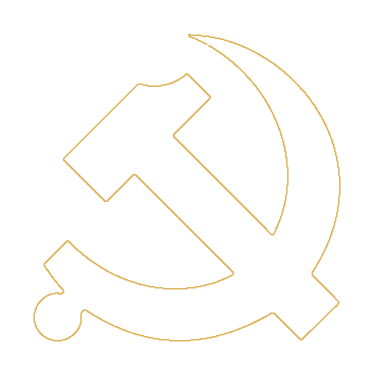

```mathematica
Graphics[{ColorData["DarkRainbow"][RandomReal[]], Line[#]}& /@ hLines]
```

Now for each curve segment we want to find a Fourier series (of the x and y  component) that approximates the segment. The typical textbook definition of the Fourier coefficients of a function f(x) are integrals of the function multiplied by cos(k x) and sin(k x). But at this point we have sets of points, not functions. To turn them into functions that we can integrate, we make a B-spline curve of each curve segment. The parametrization variable of the B-spline curve will be the integration variable. (Using B-splines instead of piecewise linear interpolations between the points will have the additional advantage of making jagged curves smoother.)

```mathematica
Graphics[BSplineCurve[#, SplineDegree -> 6, SplineClosed -> True]& /@ hLines]
```

-Graphics-

We could find the integrals needed to obtain the Fourier coefficients by numerical integration. A faster way is to use the fast Fourier transform (FFT) to get the Fourier coefficients. 

To get more uniform curves, we perform one more step: re-parametrize the spline interpolated curve of the given curve segments by arclength. The function fourierComponents implements the B-spline curve making, the re-parametrization by arclength, and the FTT calculation to obtain the Fourier coefficient. We also take into account if a curve segment is open or closed to avoid Gibbs phenomena-related oscillations. (The above demonstration of approximating the pentagram nicely shows the Gibbs phenomenon in case the “Closed” checkbox is unchecked.)

```mathematica
(* Fourier coefficients of a single curve *)
fourierComponentData[pointList_, nMax_, op_] := 
Module[{ε=10^-3, μ = 2^14, M = 10000,s,
             scale, Δ, L , nds, sMax, if, 𝓍𝓎Function, X, Y, XFT, YFT,type},
(* prepare curve *)
scale = 1. Mean[Table[ Max[ fl/@ pointList] - Min[fl /@ pointList],{fl,{First, Last}}]];
 Δ=EuclideanDistance[First[pointList], Last[pointList]];
 L=Which[op === "Closed", type="Closed";
                                                        If[First[pointList]===Last[pointList], 
                                                           pointList,Append[pointList, First[pointList]]], 
                op === "Open",type="Open";pointList,
                 Δ==0.,type="Closed";  pointList,
                 Δ/scale<op, type="Closed"; Append[pointList, First[pointList]],
                True,  type="Open"; Join[pointList, Rest[Reverse[pointList]]]];
(* re-parametrize curve by arclength *)
𝓍𝓎Function =BSplineFunction[L, SplineDegree->4];
nds = NDSolve[{s'[t]==Sqrt[𝓍𝓎Function'[t].𝓍𝓎Function'[t]], s[0]==0},s, 
                          {t, 0, 1}, MaxSteps -> 10^5, PrecisionGoal -> 4];
(* total curve length *)
     sMax= s[1]/.nds[[1]];
     if=Interpolation[Table[{s[σ]/.nds[[1]], σ}, {σ,0, 1, 1/M}]];
X[t_Real] :=  BSplineFunction[L][Max[Min[1, if[(t +Pi)/(2Pi)sMax]] , 0]][[1]];
Y[t_Real] :=  BSplineFunction[L][Max[Min[1, if[(t +Pi)/(2Pi)sMax]] , 0]][[2]]; 
(* extract Fourier coefficients *)
{XFT, YFT} = Fourier[Table[#[N @ t], {t, -Pi+ε, Pi - ε, (2Pi-2ε)/μ}]]& /@ {X, Y};   
{type,2Pi/Sqrt[μ] *
((Transpose[Table[{Re[#], Im[#]}&[Exp[I k Pi]  #[[k+1]]], {k, 0, nMax}]]& /@ {XFT, YFT}))}  ]
```

```mathematica
Options[fourierComponents] = {"MaxOrder" -> 180, "OpenClose" -> 0.025};

fourierComponents[pointLists_,OptionsPattern[]] := 
Monitor[Table[fourierComponentData[pointLists[[k]],                           
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["MaxOrder"]],
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["OpenClose"]]],
                         {k, Length[pointLists]}],
Grid[{{Text[Style["progress calculating Fourier coefficients", Darker[Green, 0.66]]], ProgressIndicator[k/Length[pointLists]]} }, 
        Alignment -> Left, Dividers -> Center]]/; Depth[pointLists] === 4
```

```mathematica
fCs = fourierComponents[hLines, "OpenClose" -> Table["Closed", {Length[hLines]}]];
```

Multiplying the Fourier coefficients by cos(k t) and sin(k t) and summing the terms gives us the desired parametrizations of the curves.

```mathematica
makeFourierSeries[{"Closed" | "Open", {{cax_, sax_},{cay_, say_}}}, t_, n_] :=
 {Sum[If[k==0, 1/2, 1]cax[[k+1]] Cos[k t]+sax[[k+1]] Sin[k t],{k,0, Min[n, Length[cax]]}],
 Sum[If[k==0, 1/2, 1]cay[[k+1]] Cos[k t]+say[[k+1]] Sin[k t],{k, 0,Min[n, Length[cay]]}]}
```

As we want the final formula for the curves to look as short and as simple as possible, we change sums of the form a cos(k t) + b sin(k t) to A sin(k t+φ) using the function sinAmplitudeForm and round the floating-point Fourier series coefficients to nearby rationals. Instead of Piecewise, we use UnitStep in the final formula to separate the individual curve segments. The real segments we  list in explicit form, and all segments that should not be drawn are encoded through the sgn((sin(t/2))^(1/2)) term.

```mathematica
sinAmplitudeForm[kt_, {cF_, sF_}] := With[{φ = phase[cF, sF]}, Sqrt[cF^2+sF^2] Sin[kt+ φ]]

phase[cF_, sF_] := With[{T = Sqrt[cF^2+sF^2]},
With[{g = Total[Abs[Table[cF Cos[x] +sF Sin[x]-  T Sin[x+#1 ArcSin[cF/T]+#2],{x, 0, 1, 0.1}]]]&}, 
          If[g[1, 0]<   g[-1, Pi],  ArcSin[cF/T],Pi-ArcSin[cF/T]]]]
```

```mathematica
singleParametrization[fCs_, t_, n_] :=
 UnitStep[Sign[ Sqrt[Sin[t/2]]]] *
 Sum[UnitStep[t-((m -1)4Pi-Pi)]UnitStep[(m -1)4Pi + 3 Pi-t]*
({+fCs[[m,2, 1, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 1, 1, k+1]], fCs[[m,2, 1, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}],   
 +fCs[[m,2, 2, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 2, 1, k+1]], fCs[[m,2, 2, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}]} ),
{m, Length[fCs]}]
```

Now we have everything together to write down the final parametrization {x(t),y(t)}.

## Mathematica final output

The number of terms in the final Fourier Series, note that the maximum number might be limited by “MaxOrder” at the top (which is 180) :

```mathematica
nTerms = 180
```

180

```mathematica
finalCurve = Rationalize[singleParametrization[fCs, t,nTerms] ,10^-3];
```

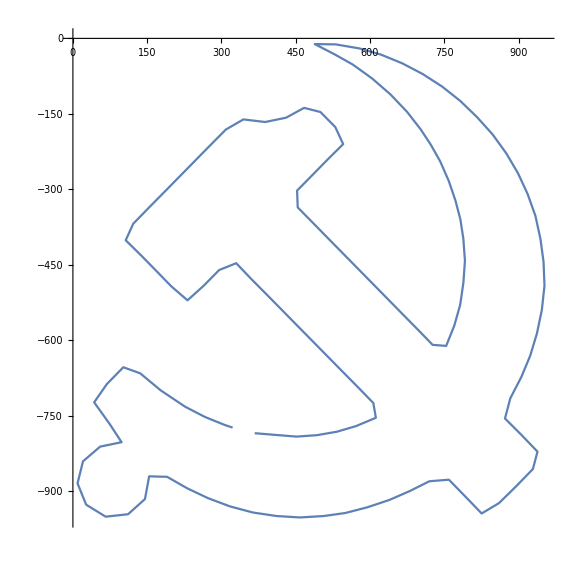

```mathematica
ParametricPlot[Evaluate[finalCurve], {t, 0,12 4Pi }]
```

## Matlab output

```mathematica
<<ToMatlab`
```

```mathematica
StringReplace[StringReplace[ToMatlab[finalCurve],"UnitStep"->"heaviside"], "Sign"->"sign"]
```

[((15581/30)+(-1/23).*sin((47/35)+(-174).*t)+(-1/24).*sin((6/25)+( ...
  -172).*t)+(-1/65).*sin((43/44)+(-170).*t)+(-1/39).*sin((41/27)+( ...
  -168).*t)+(-1/17).*sin((20/29)+(-156).*t)+(-1/84).*sin((27/23)+( ...
  -153).*t)+(-2/29).*sin((22/41)+(-146).*t)+(-1/15).*sin((18/31)+( ...
  -145).*t)+(-1/60).*sin((18/55)+(-144).*t)+(-1/29).*sin((47/43)+( ...
  -138).*t)+(-1/72).*sin((3/25)+(-137).*t)+(-1/11).*sin((24/29)+( ...
  -131).*t)+(-4/45).*sin((7/10)+(-127).*t)+(-3/37).*sin((157/105)+( ...
  -124).*t)+(-5/36).*sin((53/43)+(-121).*t)+(-7/37).*sin((49/45)+( ...
  -117).*t)+(-1/18).*sin((2/31)+(-115).*t)+(-1/7).*sin((14/9)+(-101) ...
  .*t)+(-2/25).*sin((17/13)+(-92).*t)+(-2/21).*sin((5/18)+(-90).*t)+ ...
  (-5/19).*sin((23/20)+(-88).*t)+(-1/11).*sin((59/42)+(-84).*t)+( ...
  -1/7).*sin((1/56)+(-78).*t)+(-5/17).*sin((17/15)+(-66).*t)+(-7/50) ...
  .*sin((14/31)+(-62).*t)+(-16/53).*sin((10/9)+(-59).*t)+(-11/31).* ...
  sin((23/20)+(-51).*t)+(-73/91).*sin((45/29)+(-45).*t)+(-6/23).* ...
  sin((10/31)+(-43).*t)+(-44/41).*sin((22/87)+(-39).*t)+(-13/11).* ...
  sin((43/32)+(-33).*t)+(-43/29).*sin((31/23)+(-29).*t)+(-139/25).* ...
  sin((4/13)+(-23).*t)+(-116/27).*sin((53/71)+(-22).*t)+(-1081/541) ...
  .*sin((36/25)+(-20).*t)+(-54/17).*sin((47/53)+(-19).*t)+(-79/37).* ...
  sin((7/22)+(-13).*t)+(-2064/127).*sin((17/32)+(-9).*t)+(-1319/25) ...
  .*sin((64/41)+(-6).*t)+(-2834/25).*sin((3/14)+(-2).*t)+(15176/51) ...
  .*sin((57/13)+t)+(4037/21).*sin((18/23)+3.*t)+(1247/28).*sin(( ...
  1/70)+4.*t)+(1839/31).*sin((11/26)+5.*t)+(263/21).*sin((34/19)+7.* ...
  t)+(63/20).*sin((27/13)+8.*t)+(335/29).*sin((572/127)+10.*t)+( ...
  239/38).*sin((77/51)+11.*t)+(232/25).*sin((123/28)+12.*t)+(434/37) ...
  .*sin((93/38)+14.*t)+(347/45).*sin((11/7)+15.*t)+(91/30).*sin(( ...
  32/7)+16.*t)+(141/29).*sin((91/34)+17.*t)+(309/34).*sin((146/49)+ ...
  18.*t)+(21/11).*sin((9/31)+21.*t)+(89/32).*sin((145/79)+24.*t)+( ...
  61/28).*sin((33/37)+25.*t)+(47/29).*sin((3/16)+26.*t)+(3/11).*sin( ...
  (25/23)+27.*t)+(119/41).*sin((135/44)+28.*t)+(27/19).*sin((71/24)+ ...
  30.*t)+(20/11).*sin((71/23)+31.*t)+(21/20).*sin((67/21)+32.*t)+( ...
  37/21).*sin((89/27)+34.*t)+(31/21).*sin((128/29)+35.*t)+(19/35).* ...
  sin((24/35)+36.*t)+(39/31).*sin((5/24)+37.*t)+(21/23).*sin((7/27)+ ...
  38.*t)+(51/40).*sin((39/29)+40.*t)+(5/11).*sin((22/13)+41.*t)+( ...
  14/29).*sin((25/26)+42.*t)+(11/19).*sin((29/31)+44.*t)+(20/41).* ...
  sin((47/14)+46.*t)+(16/27).*sin((97/30)+47.*t)+(5/24).*sin((37/39) ...
  +48.*t)+(20/23).*sin((95/22)+49.*t)+(4/29).*sin((117/34)+50.*t)+( ...
  4/23).*sin((9/23)+52.*t)+(7/19).*sin((25/8)+53.*t)+(10/11).*sin(( ...
  32/27)+54.*t)+(6/25).*sin((11/20)+55.*t)+(1/5).*sin((65/18)+56.*t) ...
  +(8/27).*sin((172/55)+57.*t)+(13/19).*sin((37/43)+58.*t)+(6/23).* ...
  sin((2/35)+60.*t)+(7/29).*sin((6/11)+61.*t)+(21/40).*sin((87/22)+ ...
  63.*t)+(6/23).*sin((23/34)+64.*t)+(4/25).*sin((73/33)+65.*t)+( ...
  11/40).*sin((139/34)+67.*t)+(7/26).*sin((12/7)+68.*t)+(14/25).* ...
  sin((99/32)+69.*t)+(7/48).*sin((11/3)+70.*t)+(5/22).*sin((113/47)+ ...
  71.*t)+(3/25).*sin((87/20)+72.*t)+(6/23).*sin((230/53)+73.*t)+( ...
  2/7).*sin((1/31)+74.*t)+(17/67).*sin((29/14)+75.*t)+(3/13).*sin(( ...
  35/71)+76.*t)+(7/22).*sin((7/17)+77.*t)+(8/47).*sin((145/46)+79.* ...
  t)+(7/37).*sin((1/14)+80.*t)+(11/49).*sin((36/31)+81.*t)+(4/49).* ...
  sin((157/45)+82.*t)+(3/25).*sin((111/47)+83.*t)+(9/28).*sin(( ...
  97/28)+85.*t)+(18/41).*sin((145/38)+86.*t)+(1/21).*sin((15/61)+ ...
  87.*t)+(2/29).*sin((42/11)+89.*t)+(4/33).*sin((24/31)+91.*t)+(2/9) ...
  .*sin((39/35)+93.*t)+(9/44).*sin((9/49)+94.*t)+(5/31).*sin((5/19)+ ...
  95.*t)+(2/23).*sin((283/113)+96.*t)+(8/27).*sin((29/19)+97.*t)+( ...
  3/37).*sin((11/28)+98.*t)+(1/18).*sin((114/35)+99.*t)+(5/37).*sin( ...
  (97/26)+100.*t)+(5/28).*sin((147/34)+102.*t)+(1/27).*sin((101/32)+ ...
  103.*t)+(1/56).*sin((71/16)+104.*t)+(3/23).*sin((11/30)+105.*t)+( ...
  1/14).*sin((139/33)+106.*t)+(1/25).*sin((56/15)+107.*t)+(1/53).* ...
  sin((51/20)+108.*t)+(3/19).*sin((26/17)+109.*t)+(1/10).*sin(( ...
  35/17)+110.*t)+(3/28).*sin((12/31)+111.*t)+(3/25).*sin((93/47)+ ...
  112.*t)+(3/31).*sin((57/26)+113.*t)+(6/49).*sin((67/18)+114.*t)+( ...
  1/23).*sin((113/44)+116.*t)+(1/22).*sin((166/39)+118.*t)+(1/18).* ...
  sin((13/9)+119.*t)+(3/31).*sin((155/49)+120.*t)+(2/31).*sin(( ...
  95/36)+122.*t)+(2/33).*sin((113/25)+123.*t)+(1/20).*sin((87/26)+ ...
  125.*t)+(1/6).*sin((36/19)+126.*t)+(1/60).*sin((21/25)+128.*t)+( ...
  1/23).*sin((69/25)+129.*t)+(2/27).*sin((43/33)+130.*t)+(6/53).* ...
  sin((23/20)+132.*t)+(1/15).*sin((23/33)+133.*t)+(1/20).*sin(( ...
  20/59)+134.*t)+(1/14).*sin((107/26)+135.*t)+(5/49).*sin((42/17)+ ...
  136.*t)+(4/43).*sin((86/21)+139.*t)+(1/19).*sin((102/23)+140.*t)+( ...
  2/23).*sin((162/37)+141.*t)+(1/14).*sin((106/33)+142.*t)+(1/17).* ...
  sin((227/55)+143.*t)+(1/42).*sin((5/3)+147.*t)+(1/17).*sin((80/57) ...
  +148.*t)+(1/25).*sin((31/26)+149.*t)+(1/17).*sin((106/85)+150.*t)+ ...
  (2/23).*sin((103/26)+151.*t)+(1/16).*sin((31/38)+152.*t)+(1/39).* ...
  sin((49/11)+154.*t)+(1/32).*sin((141/31)+155.*t)+(2/31).*sin(( ...
  227/54)+157.*t)+(1/35).*sin((38/9)+158.*t)+(1/22).*sin((11/35)+ ...
  159.*t)+(2/21).*sin((11/31)+160.*t)+(1/22).*sin((73/27)+161.*t)+( ...
  3/40).*sin((2/33)+162.*t)+(2/27).*sin((47/32)+163.*t)+(2/33).*sin( ...
  (66/25)+164.*t)+(2/33).*sin((38/17)+165.*t)+(4/29).*sin((48/55)+ ...
  166.*t)+(1/62).*sin((129/46)+167.*t)+(1/12).*sin((51/35)+169.*t)+( ...
  1/50).*sin((145/47)+171.*t)+(1/78).*sin((2/17)+173.*t)+(2/37).* ...
  sin((165/38)+175.*t)+(1/34).*sin((51/40)+176.*t)+(1/25).*sin(( ...
  1/11)+177.*t)+(2/39).*sin((64/17)+178.*t)+(1/50).*sin((6/29)+179.* ...
  t)+(2/37).*sin((137/37)+180.*t)).*heaviside(3.*pi+(-1).*t).* ...
  heaviside(pi+t).*heaviside(sign(sin((1/2).*t)).^(1/2)),((-23984/45)+ ...
  (-1/40).*sin((23/27)+(-175).*t)+(-1/23).*sin((12/25)+(-173).*t)+( ...
  -1/16).*sin((31/28)+(-169).*t)+(-1/18).*sin((30/29)+(-168).*t)+( ...
  -1/17).*sin((35/33)+(-163).*t)+(-1/33).*sin((13/24)+(-162).*t)+( ...
  -2/27).*sin((53/35)+(-161).*t)+(-1/62).*sin((49/41)+(-153).*t)+( ...
  -1/101).*sin((23/18)+(-148).*t)+(-1/12).*sin((14/27)+(-147).*t)+( ...
  -1/18).*sin((4/5)+(-143).*t)+(-1/22).*sin((16/23)+(-139).*t)+( ...
  -1/13).*sin((27/19)+(-136).*t)+(-1/41).*sin((40/27)+(-135).*t)+( ...
  -3/20).*sin((5/11)+(-121).*t)+(-7/39).*sin((3/25)+(-120).*t)+( ...
  -1/134).*sin((6/5)+(-117).*t)+(-8/37).*sin((15/44)+(-113).*t)+( ...
  -2/19).*sin((5/11)+(-105).*t)+(-7/45).*sin((15/32)+(-97).*t)+( ...
  -1/14).*sin((2/27)+(-96).*t)+(-1/7).*sin((33/25)+(-95).*t)+(-4/39) ...
  .*sin((73/53)+(-87).*t)+(-8/47).*sin((29/20)+(-74).*t)+(-3/16).* ...
  sin((7/16)+(-71).*t)+(-11/27).*sin((21/17)+(-68).*t)+(-10/17).* ...
  sin((27/19)+(-67).*t)+(-1/6).*sin((72/59)+(-55).*t)+(-5/28).*sin(( ...
  1/59)+(-48).*t)+(-5/38).*sin((3/32)+(-44).*t)+(-35/58).*sin(( ...
  37/27)+(-42).*t)+(-12/17).*sin((13/11)+(-41).*t)+(-8/11).*sin(( ...
  36/29)+(-40).*t)+(-20/19).*sin((1/8)+(-39).*t)+(-31/30).*sin(( ...
  34/33)+(-34).*t)+(-14/17).*sin((7/25)+(-32).*t)+(-50/31).*sin(( ...
  13/45)+(-27).*t)+(-119/66).*sin((26/21)+(-26).*t)+(-291/41).*sin(( ...
  29/59)+(-19).*t)+(-479/71).*sin((12/17)+(-18).*t)+(-5/11).*sin(( ...
  20/19)+(-16).*t)+(-63/19).*sin((38/29)+(-13).*t)+(-299/27).*sin(( ...
  27/20)+(-11).*t)+(-347/34).*sin((47/40)+(-10).*t)+(-1459/65).*sin( ...
  (45/34)+(-5).*t)+(-10543/31).*sin((17/20)+(-1).*t)+(2542/19).*sin( ...
  (9/14)+2.*t)+(4671/29).*sin((425/116)+3.*t)+(2833/42).*sin((47/34) ...
  +4.*t)+(692/17).*sin((106/31)+6.*t)+(1090/51).*sin((75/23)+7.*t)+( ...
  350/23).*sin((115/37)+8.*t)+(487/38).*sin((71/26)+9.*t)+(273/22).* ...
  sin((4/23)+12.*t)+(232/27).*sin((61/19)+14.*t)+(12/7).*sin(( ...
  137/35)+15.*t)+(39/37).*sin((137/91)+17.*t)+(199/31).*sin((12/59)+ ...
  20.*t)+(43/22).*sin((283/106)+21.*t)+(217/46).*sin((107/42)+22.*t) ...
  +(413/155).*sin((41/30)+23.*t)+(64/35).*sin((68/39)+24.*t)+(55/31) ...
  .*sin((77/31)+25.*t)+(19/34).*sin((31/78)+28.*t)+(61/21).*sin(( ...
  163/51)+29.*t)+(73/31).*sin((160/59)+30.*t)+(32/19).*sin((10/13)+ ...
  31.*t)+(6/25).*sin((299/100)+33.*t)+(14/37).*sin((21/26)+35.*t)+( ...
  13/40).*sin((87/43)+36.*t)+(69/34).*sin((330/97)+37.*t)+(28/31).* ...
  sin((91/31)+38.*t)+(17/32).*sin((31/27)+43.*t)+(18/41).*sin(( ...
  45/11)+45.*t)+(7/27).*sin((27/17)+46.*t)+(43/57).*sin((14/51)+47.* ...
  t)+(13/23).*sin((23/22)+49.*t)+(8/25).*sin((74/35)+50.*t)+(13/24) ...
  .*sin((77/37)+51.*t)+(5/29).*sin((143/31)+52.*t)+(21/74).*sin(( ...
  409/109)+53.*t)+(4/25).*sin((67/25)+54.*t)+(7/43).*sin((53/20)+ ...
  56.*t)+(17/37).*sin((20/17)+57.*t)+(7/48).*sin((134/39)+58.*t)+( ...
  10/31).*sin((129/35)+59.*t)+(16/43).*sin((131/28)+60.*t)+(7/30).* ...
  sin((82/21)+61.*t)+(8/55).*sin((46/17)+62.*t)+(9/32).*sin((188/43) ...
  +63.*t)+(4/19).*sin((165/68)+64.*t)+(17/41).*sin((71/89)+65.*t)+( ...
  10/39).*sin((23/5)+66.*t)+(10/49).*sin((49/44)+69.*t)+(7/23).*sin( ...
  (23/22)+70.*t)+(5/14).*sin((94/75)+72.*t)+(13/25).*sin((26/27)+ ...
  73.*t)+(10/31).*sin((170/39)+75.*t)+(3/28).*sin((344/115)+76.*t)+( ...
  17/41).*sin((23/11)+77.*t)+(5/27).*sin((37/20)+78.*t)+(2/13).*sin( ...
  (689/153)+79.*t)+(4/37).*sin((45/26)+80.*t)+(1/30).*sin((26/35)+ ...
  81.*t)+(6/19).*sin((94/21)+82.*t)+(3/14).*sin((116/25)+83.*t)+( ...
  1/8).*sin((30/31)+84.*t)+(2/7).*sin((59/27)+85.*t)+(5/27).*sin(( ...
  44/35)+86.*t)+(2/23).*sin((137/69)+88.*t)+(5/44).*sin((125/27)+ ...
  89.*t)+(3/17).*sin((84/19)+90.*t)+(1/27).*sin((78/17)+91.*t)+( ...
  1/61).*sin((47/46)+92.*t)+(1/28).*sin((124/45)+93.*t)+(1/19).*sin( ...
  (7/32)+94.*t)+(1/34).*sin((95/34)+98.*t)+(8/41).*sin((41/30)+99.* ...
  t)+(2/27).*sin((7/9)+100.*t)+(3/28).*sin((78/31)+101.*t)+(2/25).* ...
  sin((89/34)+102.*t)+(2/21).*sin((69/25)+103.*t)+(2/29).*sin(( ...
  25/14)+104.*t)+(1/37).*sin((119/45)+106.*t)+(1/11).*sin((57/29)+ ...
  107.*t)+(4/35).*sin((151/34)+108.*t)+(2/33).*sin((142/33)+109.*t)+ ...
  (1/77).*sin((126/29)+110.*t)+(3/32).*sin((31/10)+111.*t)+(8/65).* ...
  sin((1/28)+112.*t)+(3/38).*sin((49/13)+114.*t)+(1/10).*sin(( ...
  235/78)+115.*t)+(3/19).*sin((149/32)+116.*t)+(1/38).*sin((40/9)+ ...
  118.*t)+(1/19).*sin((80/31)+119.*t)+(1/16).*sin((76/29)+122.*t)+( ...
  1/24).*sin((303/79)+123.*t)+(1/32).*sin((177/38)+124.*t)+(3/23).* ...
  sin((34/25)+125.*t)+(2/19).*sin((49/26)+126.*t)+(1/19).*sin((9/10) ...
  +127.*t)+(1/17).*sin((9/31)+128.*t)+(1/47).*sin((43/22)+129.*t)+( ...
  5/29).*sin((10/3)+130.*t)+(3/41).*sin((84/23)+131.*t)+(3/32).*sin( ...
  (49/12)+132.*t)+(2/23).*sin((45/29)+133.*t)+(1/33).*sin((11/21)+ ...
  134.*t)+(4/45).*sin((99/26)+137.*t)+(1/22).*sin((127/53)+138.*t)+( ...
  1/37).*sin((107/30)+140.*t)+(2/33).*sin((31/20)+141.*t)+(1/17).* ...
  sin((29/27)+142.*t)+(1/37).*sin((43/14)+144.*t)+(1/22).*sin(( ...
  98/39)+145.*t)+(1/55).*sin((38/15)+146.*t)+(3/38).*sin((15/11)+ ...
  149.*t)+(1/22).*sin((8/23)+150.*t)+(2/35).*sin((29/23)+151.*t)+( ...
  1/31).*sin((263/81)+152.*t)+(2/37).*sin((33/29)+154.*t)+(2/33).* ...
  sin((19/14)+155.*t)+(3/32).*sin((171/52)+156.*t)+(1/13).*sin(( ...
  237/74)+157.*t)+(1/145).*sin((95/34)+158.*t)+(1/29).*sin((43/13)+ ...
  159.*t)+(1/23).*sin((65/14)+160.*t)+(2/29).*sin((25/7)+164.*t)+( ...
  1/23).*sin((100/199)+165.*t)+(1/24).*sin((30/23)+166.*t)+(1/58).* ...
  sin((95/31)+167.*t)+(1/52).*sin((53/21)+170.*t)+(2/29).*sin(( ...
  81/22)+171.*t)+(1/19).*sin((59/19)+172.*t)+(3/40).*sin((2/9)+174.* ...
  t)+(2/33).*sin((13/43)+176.*t)+(1/165).*sin((3/10)+177.*t)+(2/29) ...
  .*sin((17/13)+178.*t)+(1/26).*sin((86/29)+179.*t)+(3/29).*sin(( ...
  63/31)+180.*t)).*heaviside(3.*pi+(-1).*t).*heaviside(pi+t).* ...
  heaviside(sign(sin((1/2).*t)).^(1/2))];